# Kansas interpolation approach in 2D to solve elliptic PDEs, adding points with maximum residual

## Helper functions

```mathematica
(* Compiled function to generate Quasi-random numbers*)
randomPoints=Compile[{{n,_Integer},{low,_Real},{high,_Real},{minD,_Real}},Block[{data=RandomReal[{low,high},{1,2}],k=1,rv,temp},While[k<n,rv=RandomReal[{low,high},2];
temp=Transpose[Transpose[data]-rv];
If[Min[Sqrt[(#.#)]&/@temp]>minD,data=Join[data,{rv}];
k++;];];
data]];


(* Function to update interpolation matrix A with new point *)
newA=Function[{},
tmp={};
For[i=1,i≤ndata-1,i++,
{δ1,δ2}=Points[[i]]-Points[[ndata]];
If[i≤bpts,AppendTo[tmp,ϕ[δ1,δ2]],
AppendTo[tmp,Lϕ[δ1,δ2]]]];
Table[AppendTo[A[[k]], tmp[[k]]],{k,ndata-1}]; (* Append new right column *)
tmp={};
For[j=1,j≤ndata,j++,
{δ1,δ2}=Points[[ndata]]-Points[[j]];
AppendTo[tmp,Lϕ[δ1,δ2]]]; 
AppendTo[A,tmp];(* Append new final row *)
];


(* Function to build interpolation function *)
newPf=Function[{},
P=0;
For[i=1,i≤ndata,i++,
{ξ1,ξ2}=Points[[i]];
P=P+c[[i]]ϕ[x-ξ1,y-ξ2]];
P];
```

## Generating data

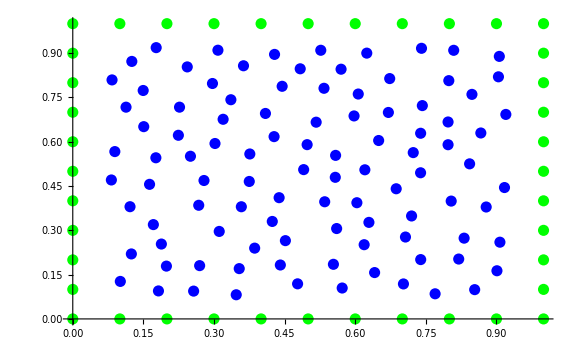

```mathematica
(* Interior Points *)
ipts=100;
minD=0.08;
low=minD;
high=1-low;
iPoints=low+(high-low)randomPoints[ipts,0.,1.,minD];

(* Boundary Points *)
bpts=40;
inf=0.;
sup=1.;
bPoints1=Table[{n/(bpts/4.),sup},{n,0,(bpts/4)-1}];
bPoints2=Table[{sup,n/(bpts/4.)},{n,1,(bpts/4)}];
bPoints3=Table[{n/(bpts/4.),inf},{n,1,(bpts/4)}];
bPoints4=Table[{inf,n/(bpts/4.)},{n,0,(bpts/4)-1}];
bPoints=Join[bPoints1,bPoints2,bPoints3,bPoints4];

(* All points *)
Points = Join[bPoints,iPoints];
ndata = ipts+bpts;

(* Plot of points *)
ListPlot[{iPoints,bPoints},ImageSize->Large,PlotStyle->{Blue,Green}]
```

## Computing laplacian of RBD

```mathematica
(* Radial basis function *)
ϵ =7.125;
r[x_,y_]=Sqrt[x^2+y^2];
ϕ[x_,y_]=Exp[-(ϵ r[x,y])^2]
Lϕ[x_,y_] =Laplacian[ϕ[x,y],{x,y}]
```

ⅇ^(-50.7656 (x^2+y^2))

-203.063 ⅇ^(-50.7656 (x^2+y^2))+10308.6 ⅇ^(-50.7656 (x^2+y^2)) x^2+10308.6 ⅇ^(-50.7656 (x^2+y^2)) y^2

## Source functions and boundary

```mathematica
u[x_, y_] = JacobiDN[π x, 0.5] JacobiDN[π y/2, 0.5];
(*u[x_,y_] = (x^3 + y^3)/6;*)
f[x_, y_] = Laplacian[u[x,y],{x,y}];
g1[x_] = u[x,1];
g2[y_] = u[1,y];
g3[x_] = u[x,0];
g4[y_] = u[0,y];
Plot3D[u[x, y], {x, 0, 1}, {y, 0, 1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]
Plot3D[f[x, y], {x, 0, 1}, {y, 0, 1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]
```

-Graphics3D-

-Graphics3D-

## Building interpolation matrix A

```mathematica
(* Filling interpolation matrix A *)
A=RandomReal[{0,1},{ndata,ndata}];

(* Sub matrix A *)
For[i=1,i≤bpts,i++,
For[j=1,j≤ndata,j++,
{δ1,δ2}=Points[[i]]-Points[[j]];
A[[i,j]]=ϕ[δ1,δ2]
]
]

(* Sub matrix A_laplace *)
For[i=bpts+1,i≤ndata,i++,
For[j=1,j≤ndata,j++,
{δ1,δ2}=Points[[i]]-Points[[j]];
A[[i,j]]=Lϕ[δ1,δ2]
]
]
```

## Some characteristics of A

4.91146×10^180

61820.9

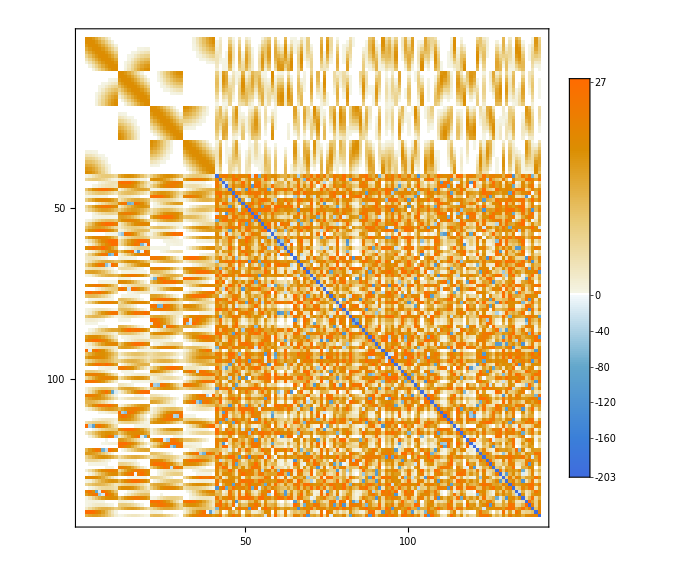

```mathematica
(* Matrix extra data *)
Det[A]
LinearAlgebra`MatrixConditionNumber[A,Norm->Infinity]
MatrixPlot[A,PlotTheme->"Detailed",ImageSize->Large]
```

## Building v: Ac=v

```mathematica
v={};
For[i=1,i≤ndata,i++,
{px,py}=Points[[i]];
If[i≤bpts/4,AppendTo[v,g1[px]],
If[i≤bpts/2,AppendTo[v,g2[py]],
If[i≤3bpts/4,AppendTo[v,g3[px]],
If[i≤bpts,AppendTo[v,g4[py]],
AppendTo[v,f[px,py]]
]]]]
];
```

## Solving linear system with GMRES method

```mathematica
(* Solving the linear system *)
c=LinearSolve[A,v,Method->{"Krylov",Method->"GMRES","Preconditioner"->"ILUTP"}];
```

## Building interplation function and error function

```mathematica
(* Interpolation function *)
Clear[x,y];
P=0;
For[i=1,i≤ndata,i++,
{ξ1,ξ2}=Points[[i]];
P=P+c[[i]]ϕ[x-ξ1,y-ξ2]
]
Pf[x_,y_]=P;
LPf[x_,y_]=Laplacian[Pf[x,y],{x,y}];
Error[x_,y_]=Pf[x,y]-u[x,y];

Plot3D[Pf[x, y], {x, 0, 1}, {y, 0, 1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]
Plot3D[Error[x,y], {x, 0, 1}, {y, 0, 1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]
```

-Graphics3D-

-Graphics3D-

## Main loop: adding points with maximum residual

```mathematica
(* Main Block *)
Input["Continue?"]; (* Waiting *)
stop=0;
count=0;
addedPoints={};
rmsError={};
maxError={};
condNumbers={};
resolvTimes={};
```

{0.0545776,0.0569377}

{0.239985,0.292012}

{0.919094,0.569056}

{0.0767708,0.199706}

{0.0805132,0.675773}

{0.95038,0.947971}

{0.0661132,0.376233}

{0.639419,0.0821842}

{0.937878,0.236375}

{0.760445,0.0591177}

10 th iteration

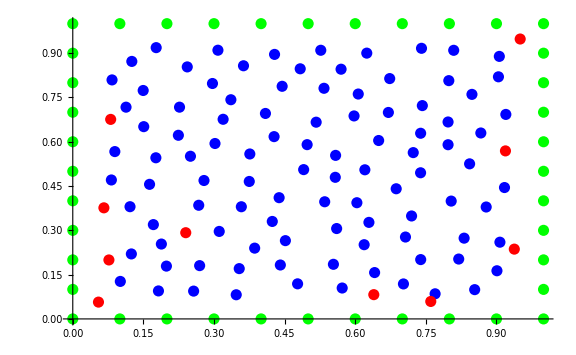

-Graphics3D-

-Graphics3D-

{0.916376,0.338719}

{0.813881,0.142723}

{0.79819,0.489193}

{0.945126,0.633884}

{0.943571,0.804039}

{0.946644,0.507645}

{0.824242,0.591553}

{0.944801,0.383971}

{0.843629,0.456259}

{0.0548302,0.943385}

20 th iteration

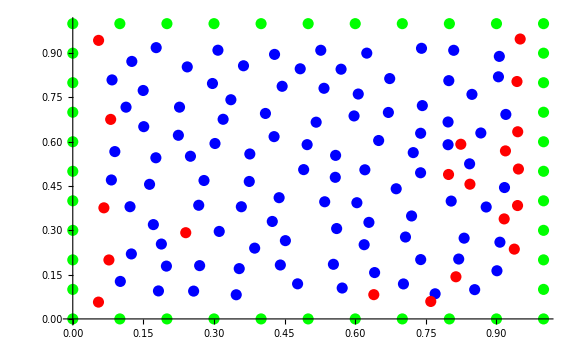

-Graphics3D-

-Graphics3D-

{0.819028,0.713094}

{0.85188,0.852546}

{0.316777,0.223775}

{0.704286,0.771069}

{0.488707,0.0633314}

{0.795158,0.947764}

{0.729321,0.843652}

{0.166265,0.708454}

{0.186545,0.819723}

{0.312084,0.527769}

30 th iteration

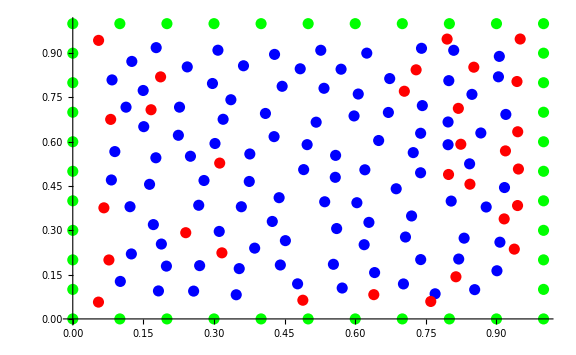

-Graphics3D-

-Graphics3D-

{0.0572336,0.715587}

{0.573224,0.623576}

{0.463174,0.937496}

{0.191663,0.407769}

{0.843699,0.562642}

{0.850387,0.702264}

{0.745617,0.429241}

{0.94993,0.0527063}

{0.949373,0.727336}

{0.957249,0.859276}

40 th iteration

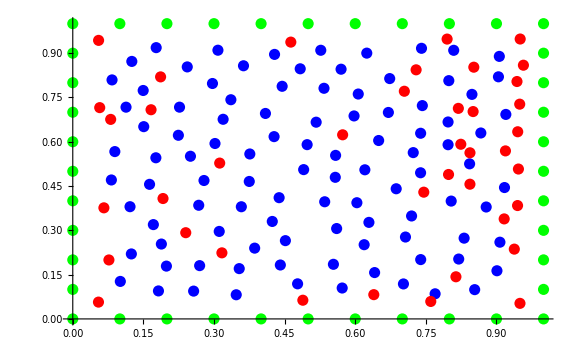

-Graphics3D-

-Graphics3D-

{0.955,0.186446}

{0.95265,0.28197}

{0.851389,0.315798}

{0.765834,0.341138}

{0.858318,0.523616}

{0.358995,0.938571}

{0.609414,0.940524}

{0.634205,0.827523}

{0.67628,0.900098}

{0.482449,0.722544}

50 th iteration

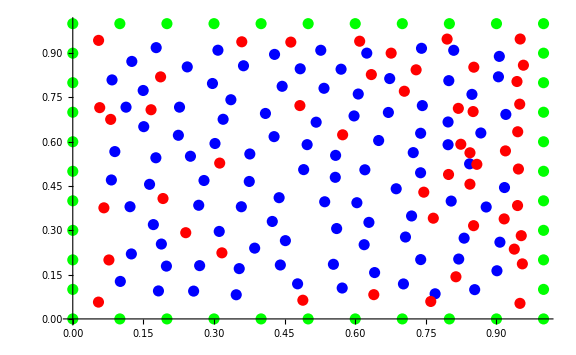

-Graphics3D-

-Graphics3D-

{0.653829,0.480897}

{0.323139,0.409867}

{0.0299085,0.0283626}

{0.148552,0.0558592}

{0.0852169,0.274873}

{0.0463113,0.140875}

{0.462713,0.456628}

{0.0418704,0.248356}

{0.213107,0.481827}

{0.492226,0.320523}

60 th iteration

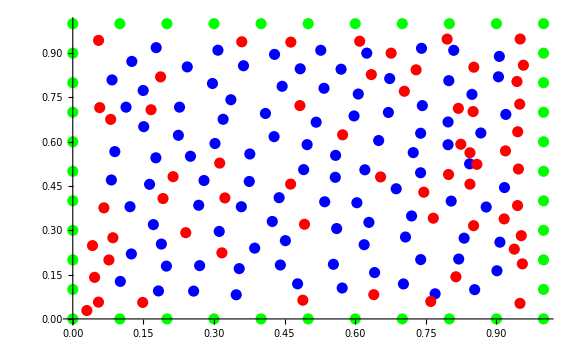

-Graphics3D-

-Graphics3D-

{0.0484279,0.535557}

{0.503588,0.444996}

{0.422957,0.506021}

{0.0461377,0.442104}

{0.228966,0.448217}

{0.133169,0.516764}

{0.266403,0.665951}

{0.361361,0.642188}

{0.25189,0.945482}

{0.40221,0.0601805}

70 th iteration

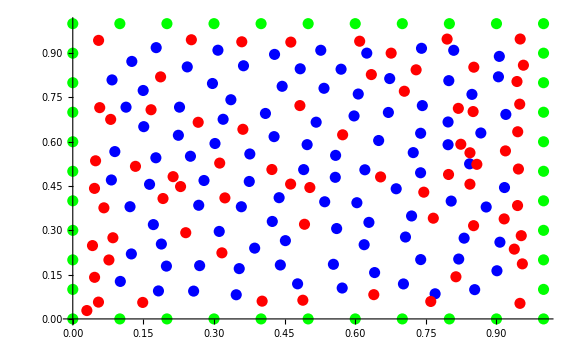

-Graphics3D-

-Graphics3D-

{0.678261,0.190829}

{0.0564708,0.645878}

{0.663712,0.415034}

{0.64179,0.559372}

{0.765793,0.765777}

{0.0284244,0.352161}

{0.649579,0.755433}

{0.547119,0.723072}

{0.706677,0.536142}

{0.767164,0.542012}

80 th iteration

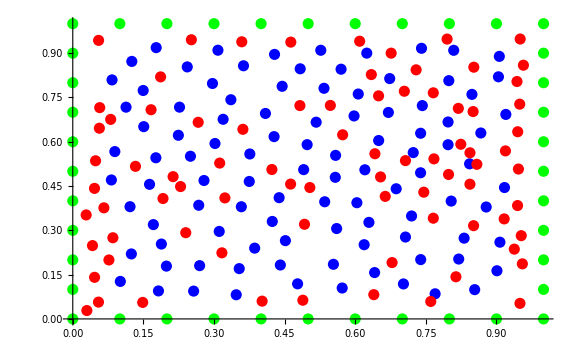

-Graphics3D-

-Graphics3D-

{0.822054,0.041696}

{0.958529,0.565587}

{0.738029,0.256011}

{0.967783,0.447673}

{0.177579,0.961413}

{0.403317,0.956713}

{0.588363,0.729229}

{0.444519,0.540778}

{0.214983,0.574297}

{0.862326,0.481205}

90 th iteration

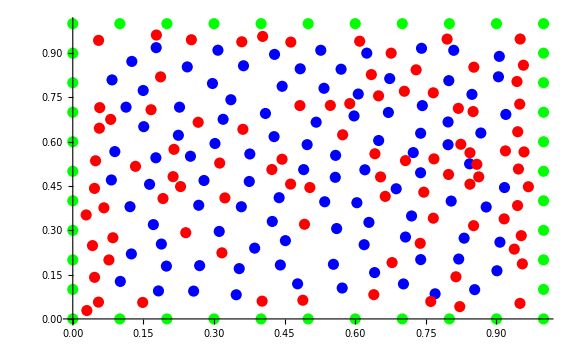

-Graphics3D-

-Graphics3D-

{0.982707,0.969571}

{0.878654,0.941468}

{0.879729,0.768464}

{0.823935,0.656583}

{0.971105,0.666022}

{0.960164,1.}

{0.952919,1.}

{0.767765,0.872844}

{0.712665,0.670477}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{0.517733,0.953091}

100 th iteration

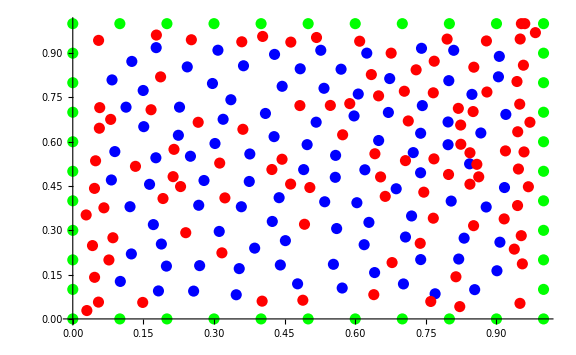

-Graphics3D-

-Graphics3D-

```mathematica
While[stop≠1,
(* Point with maximum error *)
nPoint=ArgMax[{Abs[Error[x,y]],0≤x≤1 && 0≤y≤1},{x,y}]; 
Print[nPoint];
AppendTo[Points,nPoint];
AppendTo[addedPoints,nPoint];
ndata++;

(* Recalculate A *)
newA[];
AppendTo[condNumbers,LinearAlgebra`MatrixConditionNumber[A,Norm->Infinity]];

(* Extend vector of values v *)
{px,py}=nPoint;
AppendTo[v,f[px,py]];

(* Calculate new solution *)
result=Timing[c=LinearSolve[A,v,Method->{"Krylov",Method->"GMRES","Preconditioner"->"ILUTP"}]];
AppendTo[resolvTimes,result[[1]]];

(* Build interpolation function *)
Pf[x_,y_]=newPf[];
Error[x_,y_]=Pf[x,y]-u[x,y];

(* Calculate Errors *)
(*AppendTo[rmsError,∫_0^1 ∫_0^1 (Pf[x,y]-u[x,y])^2ⅆyⅆx]; too expensive for now*)
AppendTo[maxError,Abs[Error[px,py]]];

count++;
If[Mod[count,10]==0,Print[Style[count"th iteration",25,Blue]]];
If[Mod[count,10]==0,Print[ListPlot[{iPoints,bPoints,addedPoints},ImageSize->Large,PlotStyle->{Blue,Green,Red}]]];
If[Mod[count,10]==0,Print[Plot3D[Pf[x, y], {x, 0, 1}, {y, 0, 1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]]];
If[Mod[count,10]==0,Print[Plot3D[Error[x,y], {x, 0, 1}, {y, 0, 1},PlotRange->All,PlotTheme->"Detailed",ImageSize->Large]]];
If[Mod[count,10]==0,stop=Input["Stop?"]];
]
```

## Some statistics

Max errors in each iterarion

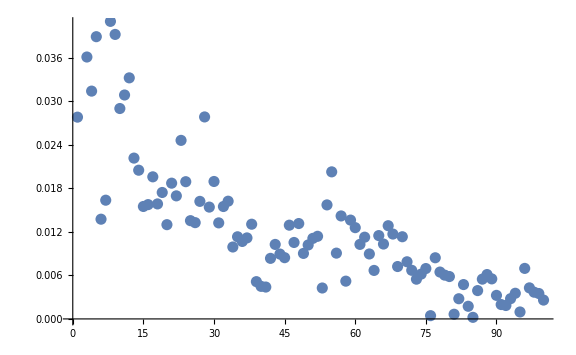

Condition numbers of A in each iteration

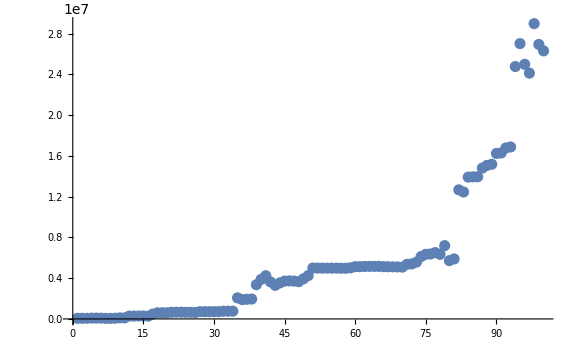

Time taken by LinearSolve in each iterarion

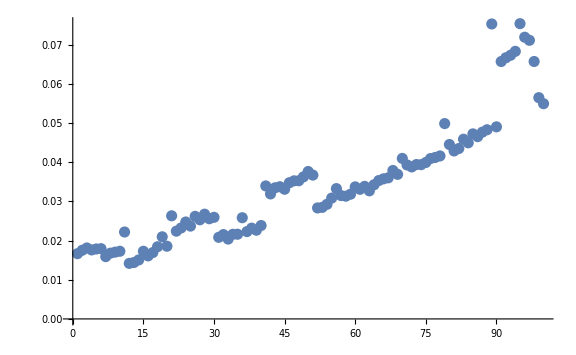

103.767 MB: Max memory usage in session

```mathematica
(* Some statistics *)
Print[Style["Max errors in each iterarion",25,Blue]]
ListPlot[maxError,ImageSize->Large]
Print[Style["Condition numbers of A in each iteration",25,Blue]]
ListPlot[condNumbers,ImageSize->Large]
Print[Style["Time taken by LinearSolve in each iterarion",25,Blue]]
ListPlot[resolvTimes,ImageSize->Large]
Print[Style["MB: Max memory usage in session "N[MaxMemoryUsed[]/2^20],25,Blue]]
(*Print[Style["Initial RMS error: "∫_0^1 ∫_0^1 Error0[x,y]^2ⅆyⅆx//N,25,Blue]]
Print[Style["Final RMS error: "∫_0^1 ∫_0^1 Error[x,y]^2ⅆyⅆx//N,25,Blue]] too hard again *)
```